```mathematica
Terminals = {x}
Terminals = Map[Function[{#,0}],Terminals]
(*Functions = {{GPlus,2},{GSubtract,2},{GDivide,2},{GTimes,2},{GExp,1},{GLog,1}}*)
Functions = {{GPlus,2},{GSubtract,2},{GDivide,2},{GTimes,2}}
FunctionTranslation={GPlus->Plus,GSubtract->Subtract,GDivide->SafeDivide,GTimes->Times,GExp->SafeExp,GLog->SafeLog}
DisplayTranslation={GPlus->Plus,GSubtract->Subtract,GDivide->Divide,GTimes->Times,GExp->Exp,GLog->Log}
SafeDivide[x_,y_]:=If[y==0,1,x/y]
SafeLog[x_]:=If[x==0,1,If[x<0,Log[-x],Log[x]]]
SafeExp[x_]:=Exp[Max[-1.*10^8,Min[1.*10^8,x]]]
```

{x}

{{x,0}}

{{GPlus,2},{GSubtract,2},{GDivide,2},{GTimes,2}}

{GPlus→Plus,GSubtract→Subtract,GDivide→SafeDivide,GTimes→Times,GExp→SafeExp,GLog→SafeLog}

{GPlus→Plus,GSubtract→Subtract,GDivide→Divide,GTimes→Times,GExp→Exp,GLog→Log}

```mathematica
TestNodeAtPoint[node_,xypair_]:=N[(xypair[[2]]-node/.FunctionTranslation/.{x->xypair[[1]]})^2]
TestNode[node_,dataset_]:=Sqrt[Total[Map[Function[pair,TestNodeAtPoint[node,pair]],dataset]]]
```

```mathematica
CalculateRawFitness[generation_]:=ParallelMap[Function[node,TestNode[node,DataPoints]],generation]
```

```mathematica
TargetFunction[x_]:=x^4+x^3+x^2+x
DataPoints=Map[Function[x,List[x,TargetFunction[x]]],Table[RandomReal[{-20,20}],{30}]];
```

```mathematica
myMaxInitDepth=5;
myMaxComplexity=200;
myGenSize=100;
myCrossoverProbability=0.9;
myMutationProbability=0.1;
```

```mathematica
myFirstGen=Table[CreateTree[myMaxComplexity,myMaxInitDepth],{myGenSize}];
myFirstGenList=Map[NodeToList,myFirstGen];
myCurrentGen=1;
```

```mathematica
myFirstGenFitness=CalculateFitness[myFirstGen];
```

```mathematica
myFirstGenBestPosition=Ordering[myFirstGenFitness,-1][[1]];
myBestFind={myCurrentGen,myFirstGenFitness[[myFirstGenBestPosition]],myFirstGen[[myFirstGenBestPosition]]};
myFirstGen[[myFirstGenBestPosition]]/.DisplayTranslation
```

x+x^4

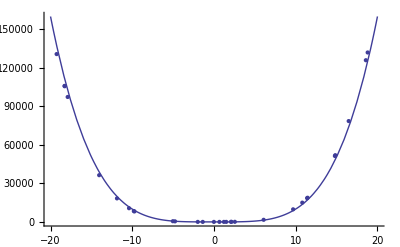

```mathematica
Show[ListPlot[DataPoints],Plot[(myBestFind[[3]]/.FunctionTranslation/.x->xvar),{xvar,-20,20}]]
```

```mathematica
myPreviousGenList=myFirstGenList;
myPreviousGenFitness=myFirstGenFitness;
```

Generation = 9

Best this generation = fitness=1. f(x)=x+x^2+x^2 (x+x^2)

Best ever = Gen=3 fitness=0.000987822 f(x)=x^2 (x+x^2)

Real = f(x)=x+x^2+x^3+x^4

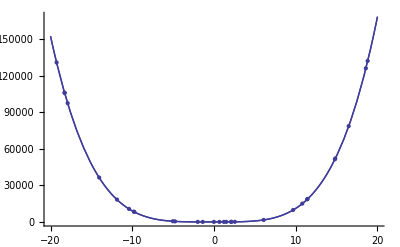

```mathematica
myCurrentGen=myCurrentGen+1;
Print["Generation = ",myCurrentGen];
myNextGenList=RandomChoice[myPreviousGenFitness->myPreviousGenList,myGenSize];
myNextGenList=ParallelBreedNodeList[myNextGenList,myCrossoverProbability,myMutationProbability,myMaxComplexity,myMaxInitDepth];
myNextGen=Map[ListToNode,myNextGenList];
myNextGenFitness=CalculateFitness[myNextGen];
myNextGenBestPosition=Ordering[myNextGenFitness,-1][[1]];
Print["Best this generation = ","fitness=",myNextGenFitness[[myNextGenBestPosition]]," f(x)=",myNextGen[[myNextGenBestPosition]]/.DisplayTranslation];
Print["Best ever = ","Gen=",myBestFind[[1]]," fitness=",myBestFind[[2]]," f(x)=",myBestFind[[3]]/.DisplayTranslation];
Print["Real = f(x)=",TargetFunction[x]];
Show[ListPlot[DataPoints],Plot[({myBestFind[[3]],myNextGen[[myNextGenBestPosition]]}/.FunctionTranslation/.x->xvar),{xvar,-20,20}]]
If[myNextGenFitness[[myNextGenBestPosition]]>myBestFind[[2]],myBestFind={myCurrentGen,myNextGenFitness[[myNextGenBestPosition]],myNextGen[[myNextGenBestPosition]]}];
myPreviousGenList=myNextGenList;
myPreviousGenFitness=myNextGenFitness;
```